```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Temp\kobzar\VM2D\settings\airfoils

```mathematica
n=1000;
```

```mathematica
Pts=N[Table[N[1/2{Cos[(2π)/n(i-1.0)],0.3Sin[(2π)/n(i-1.0)]}],{i,1,n}],16];
```

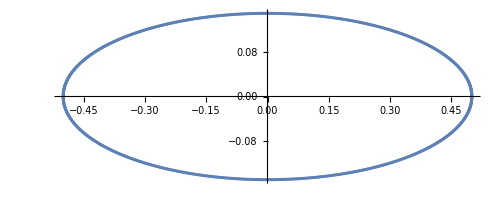

```mathematica
ListPlot[Pts,AspectRatio->Automatic]
```

```mathematica
Export["ecircle"<>ToString[n],
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.12   |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2024/01/14     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2024 I. Marchevsky, K. Sokol, E. Ryatina, A. Kolganova   |
*-----------------------------------------------------------------------------*
| File name: circle"<>TextString[n]<>StringRepeat[" ",59-StringLength@ToString[n]]<>"|
| Info: Circular airfoil ("<>TextString[n]<>" panels)"<>StringRepeat[" ",44-StringLength@ToString[n]]<>"|
\\*---------------------------------------------------------------------------*/
"}~Join~{"r = {"}~Join~((TextString[#]<>",")&/@(SetAccuracy[Pts[[1;;-2]],16]))~Join~((TextString[#])&/@(SetAccuracy[Pts[[{-1}]],16]))~Join~{" };"},"Table"]
```

ecircle1000